```mathematica
(*Name:Tommy Lee Truong
Last Edit: Nov 4 2016
Program Name: Assignment 1*)
```

# Assignment 1

What is (2^3)^4? What is 2^(3^4)? What is 2^(3^4)?

```mathematica
(2^3)^4
```

4096

```mathematica
2^(3^4)
```

2417851639229258349412352

```mathematica
2^3^4
```

2417851639229258349412352

Which is bigger, ⅇ^πor π^ⅇ?

```mathematica
N[E^Pi]
```

23.1407

```mathematica
N[Pi^E]
```

22.4592

```mathematica
ⅇ^π is bigger
```

bigger ⅇ^π is

Create a constant called myPi, and set it equal to 3.14. What is the percent error between this value of pi and the actual value?

```mathematica
myPi:=3.14
```

```mathematica
N[((Pi-myPi)/Pi)*100]
```

0.0506957

```mathematica
there is approximately a 0.05 % error
```

0.00253479 a approximately error is there

What fraction does 1/500-1/401 reduce to? What decimal is this equal to out to the 18th decimal point?

```mathematica
N[((1/500)-(1/401)),18]
```

-0.000493765586034912718

The ideal gas law is a formula that relates the temperature T, pressure P, volume V, and number of moles of a gas n, and takes the form PV=nRT, where R is a constant. A useful extension of this formula is the Van der Waals equation, which takes the form RT=(P+(a(n/V))^2)(V/n-b), where a and b are constants that depend on the specific gas (oxygen vs. argon, for example). Use Mathematica’s built-in Solve function to solve the Van der Waals equation for pressure, as well as for volume. How much would it suck to do that with a pen and paper?

```mathematica
Solve[RT==((P+a(n/V)^2)((V/n)-b)),P]
```

{{P→-(n (a b n^2-a n V+RT V^2))/((b n-V) V^2)}}

```mathematica
Solve[RT==((P+a(n/V)^2)((V/n)-b)),V]
```

{{V→(b n P+n RT)/(3 P)+(2^(1/3) (3 a n^2 P-(b n P+n RT)^2))/(3 P (-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3))-1/(3 2^(1/3) P)(-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3)},{V→(b n P+n RT)/(3 P)-((1+ⅈ √3) (3 a n^2 P-(b n P+n RT)^2))/(3 2^(2/3) P (-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3))+1/(6 2^(1/3) P)(1-ⅈ √3) (-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3)},{V→(b n P+n RT)/(3 P)-((1-ⅈ √3) (3 a n^2 P-(b n P+n RT)^2))/(3 2^(2/3) P (-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3))+1/(6 2^(1/3) P)(1+ⅈ √3) (-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3+√((-18 a b n^3 P^2-2 b^3 n^3 P^3+9 a n^3 P RT-6 b^2 n^3 P^2 RT-6 b n^3 P RT^2-2 n^3 RT^3)^2+4 (3 a n^2 P-(b n P+n RT)^2)^3))^(1/3)}}

```mathematica
alot
```

alot

One of the earliest theories that gave rise to quantum mechanics is Planck’s theory of blackbody radiation. By requiring energy to be quantized, Planck derived a relationship that described how the spectral radiance of a hot object at different wavelengths depended on the temperature of the object. This relationship is known as Planck’s distribution law, and is f(λ)=(2 hc^2)/λ^5 1/(ⅇ^(hc/λkT)-1) , where h = Planck’s constant (6.626x10^-34 J s), c = the speed of light (3.00x10^8 m/s), k is Boltzmann’s constant (1.381x10^-23 J/K), λ is the wavelength of light, and T is the absolute temperature. Prior to Planck’s breakthrough, the best theory relating the spectral radiance of a hot object at different wavelengths to the temperature of the object was the Rayleigh-Jeans law, g(λ)=(2ckT)/λ^4. Define constants for h, c, and k, and then define two functions, one for Planck’s distribution law and one for the Rayleigh-Jeans law, that take wavelength and temperature as inputs and returns the spectral radiance.

```mathematica
h:=6.626*10^(-34)
```

```mathematica
h
```

6.626×10^-34

```mathematica
c:=3.00*10^(8)
```

```mathematica
c
```

3.×10^8

```mathematica
k:=1.381*10^(-23)
```

```mathematica
k
```

1.381×10^-23

```mathematica
F[λ_,T_]:=((2h*c^(2))/(λ^5))*((1)/(ⅇ^((h*c)/(λ*k*T))-1))
```

```mathematica
F[λ_,T_]
```

(1.19268×10^-16)/((-1+ⅇ^(0.0143939/(T_ λ_))) λ_^5)

```mathematica
G[λ_,T_]:=(2c*k*T)/(λ^(4))
```

```mathematica
G[λ_,T_]
```

(8.286×10^-15 T_)/λ_^4

```mathematica
(8.286000000000001*^-15 T_)/λ_^4
```

(8.286×10^-15 T_)/λ_^4

Graph the two functions you’ve just defined on the same plot over the range 0 ≤ λ ≤ 2x10^-6m, both in black with a solid line for Planck’s distribution law and a dashed line for the Rayleigh-Jeans law, for an object with a temperature of 5,800 K (the surface temperature of the sun). Set the y-axis range to be between 0 and 5x10^13, label the x-axis “Lambda”, the y-axis “Radiance”, the solid curve “Planck”, and the dashed curve “Classical”.

```mathematica
h:=6.626*10^(-34)
```

```mathematica
h
```

6.626×10^-34

```mathematica
c:=3.00*10^(8)
```

```mathematica
c
```

3.×10^8

```mathematica
k:=1.381*10^(-23)
```

```mathematica
k
```

1.381×10^-23

```mathematica
F[λ_,T_]:=((2h*c^(2))/(λ^5))*((1)/(ⅇ^((h*c)/(λ*k*T))-1))
```

```mathematica
G[λ_,T_]:=(2c*k*T)/(λ^(4))
```

```mathematica
F[λ,T]
```

(1.19268×10^-16)/((-1+ⅇ^(0.0143939/(T λ))) λ^5)

```mathematica
G[λ,T]
```

(8.286×10^-15 T)/λ^4

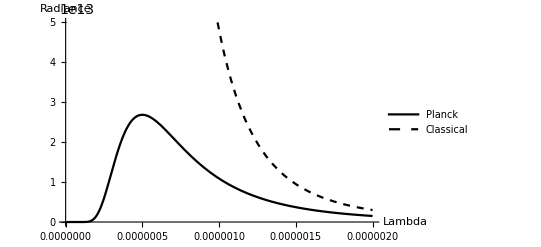

```mathematica
Plot[{F[λ,5800],G[λ,5800]},{λ,0,2*10^(-6)},PlotRange->{0,5 10^13},PlotStyle->{Black,{Black, Dashed}},AxesLabel->{Lambda,Radiance},PlotLegends->{"Planck", "Classical"}]
```